```mathematica
Cargando la red del gusano
```

```mathematica
redneuralgusano=Import["C:\\Users\\usuario\\Documents\\Trabajo de Grado II\\RedesDeAnalisis\\celegansneural\\celegansneural.gml"];
```

```mathematica
Numero de nodos
```

```mathematica
nodos=VertexCount[redneuralgusano]
```

297

```mathematica
Numero de conexiones
```

```mathematica
enlaces=EdgeCount[redneuralgusano]
```

2359

```mathematica
Histograma de la cantidad del tamaño de grupos en la red del gusano
```

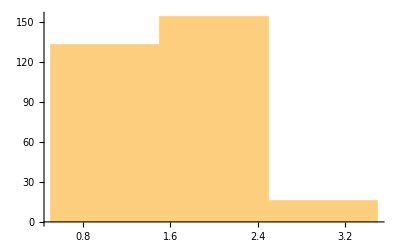

```mathematica
Histogram[Map[Length,FindClique[redneuralgusano,Infinity,All]]]
```

## Análisis de ciclos

Función que recibe como entrada un grafo y devuelve la cantidad de ciclos de longitud 3 presentes en él

```mathematica
nGC3[g_]:=Module[{adjmatrix,matrix3,amountResult},
adjmatrix=AdjacencyMatrix[g];
matrix3=MatrixPower[adjmatrix,3];
amountResult=Tr[matrix3]/6;
Return[amountResult]
];
```

Función que recibe como entrada un grafo y encuentra la cantidad de ciclos de longitud 4

```mathematica
nGC4[g_]:=Module[{adjmatrix,matrix4, amountResult,sumatoria},
adjmatrix=AdjacencyMatrix[g];
matrix4=MatrixPower[adjmatrix,4];sumatoria=Sum[(VertexDegree[g,i]*(VertexDegree[g,i]-1)),{i,VertexCount[g]}];
amountResult=(Tr[matrix4]-(2*sumatoria)-(2*EdgeCount[g]))/8;
Return[amountResult]
];
```

Función que recibe como entrada un grafo y encuentra la cantidad de ciclos de longitud 5

```mathematica
nGC5[g_]:=Module[{adjmatrix,matrix3,matrix5, amountResult,sumatoria},
adjmatrix=AdjacencyMatrix[g];
matrix3=MatrixPower[adjmatrix,3];
matrix5=MatrixPower[adjmatrix,5];sumatoria=Sum[matrix3[[i]][[i]]*(VertexDegree[g,i]-2),{i,VertexCount[g]}];
amountResult=(Tr[matrix5]-(5*sumatoria)-(5*Tr[matrix3]))/10;
Return[amountResult]
];
```

```mathematica
ciclos3=nGC3[redneuralgusano];
```

```mathematica
ciclos4=nGC4[redneuralgusano];
```

```mathematica
ciclos5=nGC5[redneuralgusano];
```

```mathematica
Cantidad de ciclos de longitud tres
```

```mathematica
N[ciclos3]
```

215.5

```mathematica
Cantidad de ciclos de longitud cuatro
```

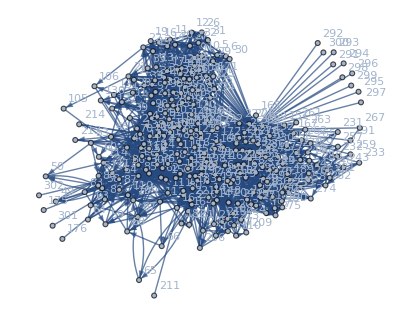
0.125 (5688.-2. (129300.+(-1.+VertexDegree[-Graphics-,297.]) VertexDegree[-Graphics-,297.]))

```mathematica
N[ciclos4]
```

```mathematica
N[ciclos5]
```

-4813.5